{α→1,γ→0.5,β→0.01}

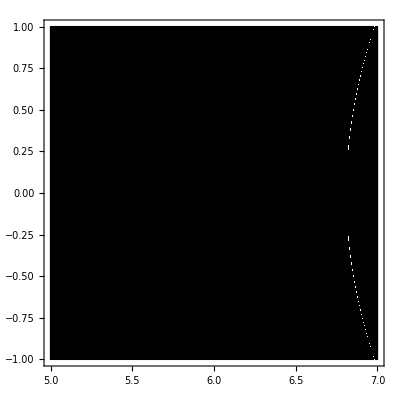

-Graphics-

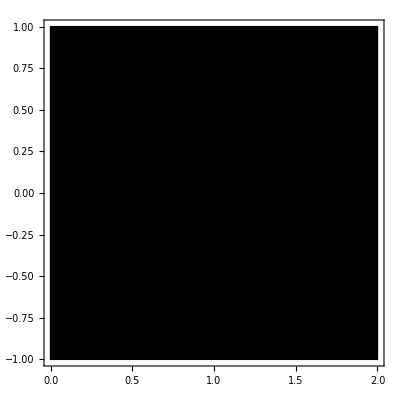

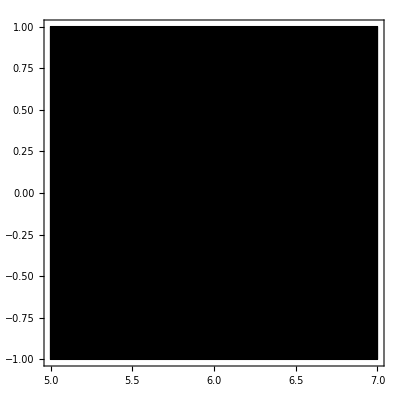

```mathematica
def={α-> 1,γ-> 0.5,β-> 0.01}
ComplexPlot[(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)/.def,{n,5-I,7+I},PlotLegends->Automatic]
ComplexPlot[(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)/.def,{n,5-I,7+I},PlotLegends->Automatic]
ComplexPlot[((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)/.{α-> 1,γ-> 0.5,β-> 0.1},{n,0-I,2+I},PlotLegends->Automatic, ColorFunction->"CyclicLogAbsArg"]
ComplexPlot[((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)/.def,{n,5-I,7+I},PlotLegends->Automatic, ColorFunction->"CyclicLogAbsArg"]
```

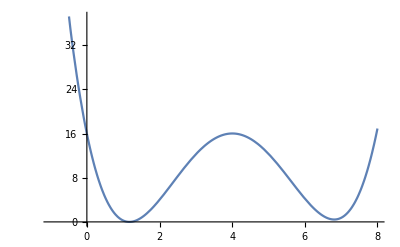

```mathematica
Plot[((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)/.def,{n,-1,8},PlotLegends->Automatic]
```

```mathematica
ComplexPlot[Log[z],{z,-2-2I,2+2I}]
```

-Graphics-

```mathematica
ComplexPlot3D[((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)/.def,{n,0-I,7+I},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
(*симметричный график дисперсии*)
Manipulate[Plot[{(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,1-m,1+m},AxesLabel->{"p_3/q","k_0^2/q^2"} ,GridLines -> Automatic],{m,2,0},{M,2,1000},{α,1,2},{β,0.5,3},{γ,1,2}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*асимметричный график дисперсии*)
Manipulate[Plot[{(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,0,1+m},AxesLabel->{"p_3/q","k_0^2/q^2"},GridLines -> Automatic,Ticks-> {{Automatic,{(2 (α-√(α γ)))/(α-γ),"m_(3; l)=1.38"}, {(2 (α+√(α γ)))/(α-γ),"m_(3; r)=3.6"}},Automatic}],{m,3,0},{M,2,1000},{α,0.5,2},{β,0.03,3},{γ,0.1,2}]
```

```mathematica
Assuming[α>γ,Solve[((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)==0,n]/.β-> 0//Simplify]
```

{{n→(2 (α-√(α γ)))/(α-γ)},{n→(2 (α-√(α γ)))/(α-γ)},{n→(2 (α+√(α γ)))/(α-γ)},{n→(2 (α+√(α γ)))/(α-γ)}}

```mathematica
(*поляризация для верхней ветви у щели*)
Manipulate[Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M/2,M},AxesLabel->{"p_3/q","ξ_2"},GridLines -> Automatic],{m,5,0},{M,3,1000},{α,1,2},{β,0.1,3},{γ,1,2}]
```

```mathematica
(*поляризация для нижней ветви у щели*)
Manipulate[Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M/2,M},AxesLabel->{"p_3/q","ξ_2"},GridLines -> Automatic],{m,5,0},{M,3,1000},{α,1,2},{β,0.1,3},{γ,1,2}]
```

```mathematica
(*поляризация для верхней ветви у щели*)
Manipulate[Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M/2,M},AxesLabel->{"p_3/q","ξ_2"}, Ticks-> {{ {(2 (α-√(α γ)))/(α-γ),"m_(3; l)"}, {(2 (α+√(α γ)))/(α-γ),"m_(3; r)=6.8"}},Automatic},GridLines -> Automatic],{m,5,0},{M,14,1000},{α,1,2},{β,0.01,3},{γ,0.5,2}]
```

```mathematica
(*поляризация для нижней ветви у щели*)
Manipulate[Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M/2,M},AxesLabel->{"p_3/q","ξ_2"},Ticks-> {{ {(2 (α-√(α γ)))/(α-γ),"m_(3; l)"}, {(2 (α+√(α γ)))/(α-γ),"m_(3; r)=6.8"}},Automatic},GridLines -> Automatic],{m,5,0},{M,14,1000},{α,1,2},{β,0.01,3},{γ,0.5,2}]
```

```mathematica
ParametricPlot3D[{{Sin[z],Cos[z],z/5},{2Sin[z],2Cos[z],z/5}},{z,0,8π}]
```

-Graphics3D-